```mathematica
img=Import["E:\\MISC\\Image\\99fb3cad6e3566c962ab10c969ae6720.jpg"]
```

-Graphics-

```mathematica
ImageCollage[Table[Blur[img,r],{r,{2,4,6,8}}],ImagePadding->3]
```

-Graphics-

```mathematica
ImageCollage[Table[EdgeDetect[Blur[img,r]],{r,{2,5,7,9,15,18}}],ImagePadding->3]
```

-Graphics-

```mathematica
ImageCollage[Table[EdgeDetect[img,r],{r,{2,5,7,9,15,18}}],ImagePadding->3]
```

-Graphics-

```mathematica
Binarize@img//Blur
```

-Graphics-

```mathematica
Manipulate[Show[fun[img,Binarize[Blur[img],t]],ImageSize->Large],{{t,0.5,"阈值"},0,1},{fun,{ImageAdd,ImageMultiply}}]
```

```mathematica
ImageMeasurements[EdgeDetect[Blur[img],4],"Contours"]
```

{Line[{{213,365},{213,364},{213,364},{209,364},{209,363},{209,363},{205,363},{205,362},{205,362},{202,362},{202,361},{202,361},{200,361},{200,360},{200,360},293,{297,360},{297,361},{295,361},{295,361},{295,362},{292,362},{292,362},{292,363},{289,363},{289,363},{289,364},{282,364},{282,364},{282,365},{213,365}}],196}
 |  |  |  |

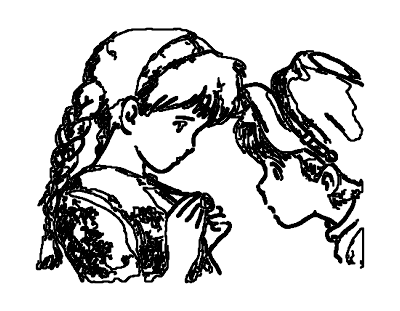

```mathematica
Graphics[ImageMeasurements[EdgeDetect[Blur[img,2],1],"Contours"]]
```

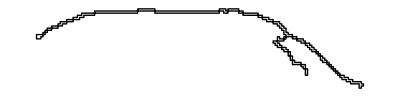

```mathematica
Graphics[ImageMeasurements[EdgeDetect[Blur[img,2],1],"Contours"][[1]]]
```

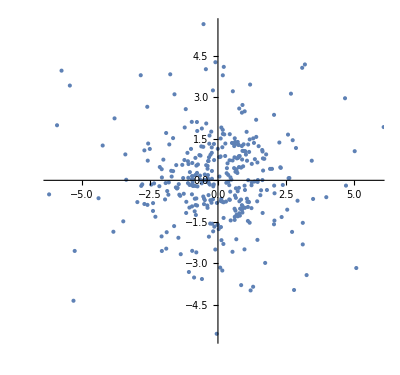

```mathematica
c=ImageMeasurements[EdgeDetect[Blur[img,2],1],"Contours"][[1,1]];
ComplexListPlot[Fourier[Complex@@@c]]
```

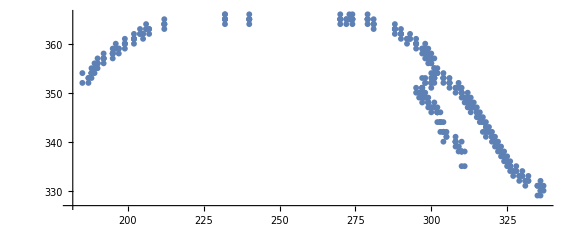

```mathematica
Show[ComplexListPlot[InverseFourier[Fourier[Complex@@@c]],PlotStyle->{PointSize[Large],Magenta}],ListPlot[c],ImageSize->Large]
```

```mathematica
dft[c_,n_]:=(z=Fourier[Complex@@@c];
k=Ceiling[Min[Length[c]/2,n]/2];
z[[k;;-k]]=0;
rc=ReIm@InverseFourier[z];
Append[rc,rc[[1]]])
```

```mathematica
Table[Show[Binarize@Blur[img],Graphics[{Gray,Line[dft[#[[1]],n]&/@ImageMeasurements[EdgeDetect[Blur[img],4],"Contours"]]}],ImageSize->Large],{n,{6,20,40}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
el=ImageMeasurements[EdgeDetect[Blur[img],4],"Contours"];g=Graphics[Table[{GrayLevel[0,n/70],AbsoluteThickness[80/n],Line[dft[#[[1]],n]&/@el]},{n,{6,8,10,15,20,25,40,100,150}}],ImageSize->Large]
```

-Graphics-

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[…]

```mathematica
Show[img,Graphics[ImageMeasurements[EdgeDetect[Blur[img],1],"Contours"]],ImageSize->Large]
```

-Graphics-